```mathematica
path="D:\\GitHubRepository\\Qubit-data-process\\PaperDataProcess\\Fluorescence shelving of a superconducting circuit\\Fluorescence\\";
```

# Sup_circles

```mathematica
file=path<>"sup_circles_data.hdf5";
data=Import[file, "Data"];
power = data["/power"]
freq = data["/freq"];
refl=data["/R_real"]+I data["/R_imag"];
```

{-10.,-5.,0.,5.,10.}

```mathematica
powerRef=0;
npower=Length[power];
nfreq=Length[freq];
MinFreq=Min[freq];
MaxFreq=Max[freq];
MinPowerInd=2;
(*don't plot -10dBm*)
MaxPowerInd=npower;
tofit=Table[{freq[[j]],10^((power[[k]]-powerRef)/10),l,l*Im@refl[[j,k]]+(1-l)*Re@refl[[j,k]]},{k,MinPowerInd,MaxPowerInd},{l,0,1},{j,1,nfreq}];
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{f0→6.54714,Γ→0.00171996,p→0.772675,α→6.11217×10^-7}

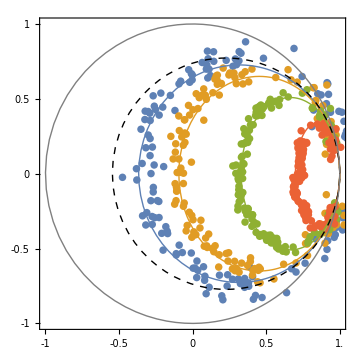

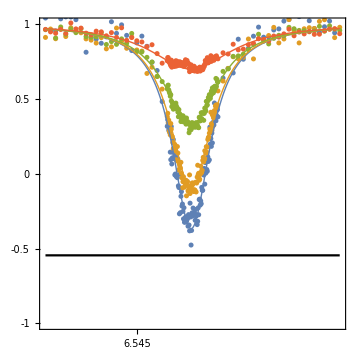

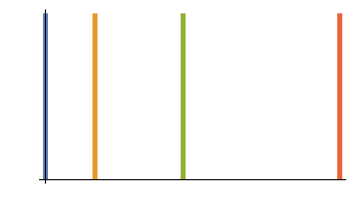

```mathematica
fit=FindFit[Flatten[tofit,2],(1-s)*Re[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α   P)]+s*Im[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α P)],{{f0,(freq[[1]]+freq[[-1]])/2},{Γ,0.00186},{p,0.793},{α,0.003}},{f,P,s}]
PlotIndices={1,2,3,4};
ΩRabi =10^3 √(α 10^((power[[MinPowerInd;;MaxPowerInd]]-powerRef)/10))/.fit;

g1=Show[ListPlot[Table[Transpose@{tofit[[i,1,;;,-1]],tofit[[i,2,;;,-1]]},{i,PlotIndices}],PlotRange->{{-1,1},{-1,1}},AspectRatio->1,PlotStyle->PointSize[0.015]],
ParametricPlot[Evaluate@Table[{Re[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α  tofit[[i,1,1,2]])],Im[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α  tofit[[i,1,1,2]])]}/.fit,{i,PlotIndices}],{f,5,8},PlotPoints->1000,PlotRange->All,PlotStyle->Thick],
ParametricPlot[Evaluate@{Re[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2)],Im[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2)]}/.fit,{f,5,8},PlotPoints->1000,PlotRange->All,PlotStyle->Directive[Black,Thick,Dashed]],
ParametricPlot[Evaluate@{Re[1-(2 Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2)],Im[1-(2  Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2)]}/.fit,{f,5,8},PlotPoints->1000,PlotRange->All,PlotStyle->Directive[Gray,Thick]]
,Frame->True,FrameTicks->{{{-1,-0.5,0,0.5,1},None},{{-1,-0.5,0,0.5,1.0},None}},FrameTicksStyle->Directive[Black,16],ImageSize->Medium]

g2=Show[ListPlot[Table[Transpose@{tofit[[i,1,;;,-4]],tofit[[i,1,;;,-1]]},{i,PlotIndices}],PlotStyle->PointSize[0.01],PlotRange->{{MinFreq,MaxFreq},{-1,1}}],Plot[Evaluate@Table[Re[1-(2 p Γ (2 I (f-f0)+Γ))/(4 (f-f0)^2+Γ^2+2α  tofit[[i,1,1,2]])]/.fit,{i,PlotIndices}],{f,MinFreq,MaxFreq},PlotRange->All,PlotStyle->Thick],
Plot[1-2p/.fit,{f,MinFreq,MaxFreq},PlotStyle->Black],Frame->True,FrameTicks->{{{-1,-0.5,0,0.5,1},None},{Table[6.53+0.005i,{i,0,10}],None}},FrameTicksStyle->Directive[Black,16],AspectRatio->1,ImageSize->Medium]


g3=ParametricPlot[Evaluate[{#,x}&/@ΩRabi],{x,-0,0.5},PlotStyle->Thickness[0.01],Ticks->{Table[i,{i,0,10}],None},TicksStyle->Directive[Black,"Arial", 14]]
```

```mathematica
Export[path<>"sup_circles.eps",g1]
Export[path<>"sup_circles_real_part.eps",g2]
Export[path<>"sup_Omega_rabi.eps",g3]
```

D:\GitHubRepository\Qubit-data-process\PaperDataProcess\Fluorescence shelving of a superconducting circuit\Fluorescence\circles.eps

D:\GitHubRepository\Qubit-data-process\PaperDataProcess\Fluorescence shelving of a superconducting circuit\Fluorescence\circles_real_part.eps

D:\GitHubRepository\Qubit-data-process\PaperDataProcess\Fluorescence shelving of a superconducting circuit\Fluorescence\Omega_rabi.eps

# Sup_rabi

```mathematica
PtSize=0.035;
```

## 01 Rabi

```mathematica
file=path<>"sup_01_rabi_data.hdf5";
data=Import[file, "Data"];
delays = data["/x"];
reflection = data["/y"];
```

{A→-0.239804,B→0.524669,Ω→0.00573018,ϕo→0.00182041,TR→-1.19484×10^17}

3.03632

87.2573

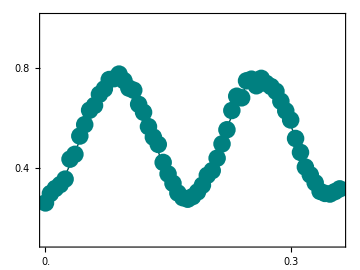

```mathematica
fit=FindFit[Transpose[{delays,reflection}],{A*Cos[2π*Ω*t+ϕo]*Exp[-t/TR]+B},{{A,-0.3},{B,0.5},{Ω,0.004},{ϕo,0},{TR,10000}},t]
Pratio01=(1-B-A)/(1-B+A)/.fit
1/(Ω)/2/.fit
g=Show[Plot[(A*Cos[2π*Ω*1000*t+ϕo]*Exp[-(1000t+ϕo)/TR]+B)/.fit,{t,0,delays[[-1]]/1000}, PlotStyle->Directive[Darker@RGBColor[0,0.5,0.5],Thick],PlotRange->{0.1,1}],ListPlot[Transpose@{delays/1000,reflection}, PlotStyle->{PointSize[PtSize],RGBColor[0,0.5,0.5]}],FrameTicks->{{Table[0.2i,{i,0,10}],None},{Table[0.1i,{i,0,10}],None}}, Frame->True, FrameTicksStyle->Directive[Black,16],ImageSize->Medium,AspectRatio->0.75]
```

```mathematica
Export[path<>"sup_01_rabi.eps",g]
```

D:\GitHubRepository\Qubit-data-process\PaperDataProcess\Fluorescence shelving of a superconducting circuit\Fluorescence\sup_01_rabi.eps

## 02 Rabi

```mathematica
file=path<>"sup_02_rabi_data.hdf5";
data=Import[file, "Data"];
delays = data["/x"];
reflection = data["/y"];
```

{A→-0.349157,B→0.621802,Ω→0.00818628,ϕo→-0.0321924,TR→1256.41}

25.0457

61.0778

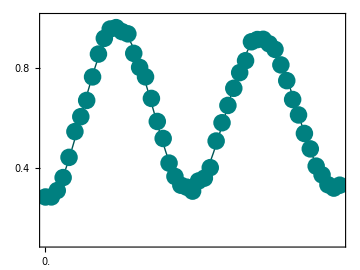

```mathematica
fit=FindFit[Transpose[{delays,reflection}],A*Cos[2π*Ω*t+ϕo]*Exp[-t/TR]+B,{{A,-0.3},{B,0.5},{Ω,0.008},{ϕo,0},{TR,1000}},t]
Pratio02=(1-B-A)/(1-B+A)/.fit
1/(Ω)/2/.fit
g=Show[Plot[(A*Cos[2π*Ω*1000*t+ϕo]*Exp[-(1000t+ϕo)/TR]+B)/.fit,{t,0,delays[[-1]]/1000}, PlotStyle->Directive[Darker@RGBColor[0,0.5,0.5],Thick],PlotRange->{0.1,1}],ListPlot[Transpose@{delays/1000,reflection}, PlotStyle->{PointSize[PtSize],RGBColor[0,0.5,0.5]}],FrameTicks->{{Table[0.2i,{i,0,10}],None},{Table[0.2i,{i,0,10}],None}}, Frame->True, FrameTicksStyle->Directive[Black,16],ImageSize->Medium,AspectRatio->0.75]
```

```mathematica
{A->-0.23980407626474043,B->0.5246690054173708,Ω->0.005730179563633806,ϕo->0.001820411095133846,TR->-1.1948380329308085*^17}
```

{A→-0.239804,B→0.524669,Ω→0.00573018,ϕo→0.00182041,TR→-1.19484×10^17}

```mathematica
Export[path<>"sup_02_rabi.eps",g]
```

D:\GitHubRepository\Qubit-data-process\PaperDataProcess\Fluorescence shelving of a superconducting circuit\Fluorescence\rabi.eps

```mathematica
1/(1+1/3.03+1/25.0457)
```

0.729948